Finite groups in Mathematica: basics

This file is an introduction to finite groups in Mathematica. The main example is S_3. 
The purpose is 1. review group theory, 2. give foundation for group algebra ℂS_3 (see notes). 
Mathematica knows groups by order, for example order 3:

```mathematica
Remove["Global`*"] //Quiet
```

```mathematica
FiniteGroupData[3]
```

(CyclicGroup | 3)

There is only one unique finite group of order 3 up to isomorphism. So it only lists one as default: the cyclic group C_3 ≃ ℤ_3. But it also knows other groups of order 3, related to C_3 by isomorphism:

```mathematica
FiniteGroupData[{"CyclicGroup",3},"IsomorphicGroups"]
```

(3 | 1
AlternatingGroup | 3
CrystallographicPointGroup | 16
PointGroup | {C,3}
SmallGroup | {3,1})

If we go up to order 6 we start seeing the symmetric group S_3:
 (in the notes, group names are written in the “𝔉𝔯𝔞𝔨𝔱𝔲𝔯” font, but I won’t use that font here)

```mathematica
FiniteGroupData[6]
```

(AbelianGroup | {3,2}
SymmetricGroup | 3)

The group S_3 is isomorphic to lots of groups, most of which we will not discuss here:

```mathematica
FiniteGroupData[{"SymmetricGroup",3},"IsomorphicGroups"]
```

(6 | 2
ChevalleyGroupB | {1,2}
CrystallographicPointGroup | 18
CrystallographicPointGroup | 19
DihedralGroup | 3
PointGroup | {Cv,3}
PointGroup | {D,3}
ProjectiveSpecialLinearGroup | {2,2}
ProjectiveSymplecticGroup | {2,2}
SmallGroup | {6,1})

To call two isomorphic groups “equal”, there should be a canonical isomorphism between them, i.e. there is some more or less “standard” way to relate them.

So far, just names. Now let’s look at how we describe groups somewhat abstractly, i.e. not yet as explicitly as in Ch.4 Representations. (“Somewhat” abstractly, since to work with these groups, in principle you don’t need to know anything more than the following.)

Example 1: cyclic group C_3 (i.e. ℤ_3). Write the elements and generators:

```mathematica
GroupElements[CyclicGroup[3]]
```

{Cycles[{}],Cycles[(1 | 2 | 3)],Cycles[(1 | 3 | 2)]}

These three operations act as follows on three objects 1,2,3:

```mathematica
PermutationReplace[{1,2,3},%]
```

(1 | 2 | 3
2 | 3 | 1
3 | 1 | 2)

So: don’t permute at all, permute cyclically once (1 → 2,  2 → 3, 3 → 1), permute cyclically twice (1 → 3,  2 → 1, 3 → 2).  (Note that there are no “reflection” that squares to the identity here like 1 → 2,  2 → 1, 3 → 3: which is not in C_3.)

```mathematica
GroupGenerators[CyclicGroup[3]]
```

{Cycles[(1 | 2 | 3)]}

There is only one generator: C_3 is an abelian group. For example, we can get the 3rd element by taking the 2nd element twice (as you can hear from “permute cyclically twice”), using Mathematica’s permutation product \[PermutationProduct] (typed as esc p* esc):

```mathematica
Cycles[{{1,2,3}}]\[PermutationProduct] Cycles[{{1,2,3}}]
```

Cycles[(1 | 3 | 2)]

Example 2: the dihedral group D_3, geometric symmetries of a triangle, has 6 elements:

```mathematica
GroupElements[DihedralGroup[3]]
```

{Cycles[{}],Cycles[(2 | 3)],Cycles[(1 | 2)],Cycles[(1 | 2 | 3)],Cycles[(1 | 3 | 2)],Cycles[(1 | 3)]}

The above ordering of the group elements is a little unexpected at first. Mathematica has its own ordering, where (1 3) is last, number 6:

```mathematica
GroupElementPosition[DihedralGroup[3],Cycles[{{1,3}}]]
```

6

Generators:

```mathematica
GroupGenerators[DihedralGroup[3]]
```

{Cycles[(2 | 3)],Cycles[(1 | 2 | 3)]}

There are two generators, and in fact D_3 is nonabelian.

Example 3: the symmetric group S_3

```mathematica
S3=SymmetricGroup[3];
GroupElements[S3]
```

{Cycles[{}],Cycles[(2 | 3)],Cycles[(1 | 2)],Cycles[(1 | 2 | 3)],Cycles[(1 | 3 | 2)],Cycles[(1 | 3)]}

The same as the dihedral group D_3 above.

```mathematica
{a,b}=GroupGenerators[S3]
GroupElementPosition[S3,%]
```

{Cycles[(1 | 2)],Cycles[(1 | 2 | 3)]}

{3,4}

These two generators of S_3 are not a and b in the notes, that both square to 1. Only number 2,3,6 here square to 1.  But we can still call these two generators a and b, they’re just not the same a and b.

As above, the permutation product is written in Mathematica as \[PermutationProduct] (esc p* esc):

```mathematica
a \[PermutationProduct] b
```

Cycles[(1 | 3)]

We find this as number 6 in the element list:

```mathematica
GroupElementPosition[S3,%]
```

6

So 3 \[PermutationProduct] 4 = 6. Here are all the possible multiplications in S_3:

```mathematica
TableForm[GroupMultiplicationTable[S3],TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | 1 | 2 | 3 | 4 | 5 | 6
2 | 2 | 1 | 4 | 3 | 6 | 5
3 | 3 | 5 | 1 | 6 | 2 | 4
4 | 4 | 6 | 2 | 5 | 1 | 3
5 | 5 | 3 | 6 | 1 | 4 | 2
6 | 6 | 4 | 5 | 2 | 3 | 1

The ordering is first row, then column. So indeed 3 \[PermutationProduct] 4 = 6. But note in the table that 4 \[PermutationProduct] 3 = 2. So multiplication in this group is not commutative. 
If we focus on the the rows and columns numbered 3 to 4 in the above table:

```mathematica
GroupMultiplicationTable[S3][[3;;4,3;;4]]
```

(1 | 6
2 | 5)

we see that indeed multiplication of just 3,4 generate all other elements: 1,2,5,6. So indeed number 3 and 4 generate the group. 

How does the above relate to the presentation by relations ⟨a,b| a^2 ,b^2, (ab)^3⟩? This means both a and b square to the unit group element e. Look at the table: for example, number 2 and 3 have this property. We see that their product c = ab is number 4. Take this to the 3rd permutation power:

```mathematica
c = GroupElements[S3][[4]];
c \[PermutationProduct] c \[PermutationProduct] c
```

Cycles[{}]

This is the unit operation, i.e. in fact c^3 = (ab)^3 = e. So number 2,3 work as a,b. Again, this is not the basis of generators that Mathematica picked, since 4 \[PermutationProduct] 4 ≠ 1. 

We can visualize the relations in the group as its Cayley graph, that Mathematica knows:

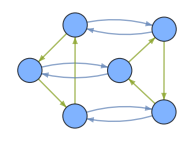

```mathematica
CayleyGraph[S3,VertexLabels->Placed["Name",Center],VertexSize->0.4]
```

Here multiplication by the element a is blue, by b is green.
We see that blue is order 2, green is order 3.

```mathematica
{PermutationOrder[a],PermutationOrder[b]}
```

{2,3}

As a final pre-defined thing, we can get the orbits explicitly:

```mathematica
GroupOrbits[S3,{1}]
```

(1 | 2 | 3)

To get a little more understanding of how Mathematica does these things, the Mathematica help page recommends the following home-made visualization of cycles. Explicitly convert to a directed graph, stored as a list of directed edges, denoted as 1->2, and so on:

Cycles[(1 | 2)]

{1->2,2->1}

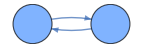

```mathematica
perm = Cycles[{{1,2}}]
rules[cycle_]:=Thread[DirectedEdge[cycle,RotateLeft[cycle]]];
Flatten[rules/@First[perm]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.5]
```

This obviously represents swapping 1 and 2.
I don’t re-display the rules when I redo this:

```mathematica
perm = Cycles[{{1,2,3}}];
```

```mathematica
rules[cycle_]:=Thread[DirectedEdge[cycle,RotateLeft[cycle]]];
Flatten[rules/@First[perm]]
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

{1->2,2->3,3->1}

-Graphics-

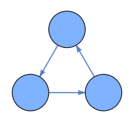

```mathematica
Graph[%,VertexLabels->Placed["Name",Center],VertexSize->0.5]
```

Now an application, the Galois group of a polynomial:

```mathematica
ResourceFunction["GaloisGroupProperties"][x^3-x +1,x]
```

SymmetricGroup[3]

Galois theory then says there is only one real root, and this is correct:

```mathematica
Solve[x^3-x +1==0,x,Reals]//First//ToRadicals
```

{x→-(2/(3 (9-√69)))^(1/3)-(1/2 (9-√69))^(1/3)/3^(2/3)}

More generally, an “irreducible” polynomial of prime degree p larger than 4 with exactly 2 nonreal roots has Galois group S_p. For more on this, see my Galois notes.

Finally, for entertainment, the biggest sporadic finite group, the Monster:

```mathematica
MonsterGroupM[]//GroupOrder
```

808017424794512875886459904961710757005754368000000000

The monster group has a faithful linear representation of dimension over the field of two elements of order 196 882. This number is decently approximated by:

```mathematica
2 π BesselI[1,4π]//N
```

196551.

For more on why this is, see my Cambridge lecture series notes (2022)
https://tp.hotell.kau.se/marcus/notes/newton.html
but this is of course not needed for this course.